## Division de l’octave en 12 parties égales :

```mathematica
Table[2^(k/12),{k,0,12}]//N
```

{1.,1.05946,1.12246,1.18921,1.25992,1.33484,1.41421,1.49831,1.5874,1.68179,1.7818,1.88775,2.}

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]              (*Cette fonction donne l'angle trigonométrique quans on donne l'écart en cents par rapport au sommet du cercle parcouru dans le sens horlogique*)
```

```mathematica
{theta[0],theta[300],theta[600],theta[900]}
```

{π/2,0,(3 π)/2,π}

## Partition de l’octave :

```mathematica
Differences[Sort[Mod[1200.Log[2,Table[NestWhile[#/2&,4/3(3/2)^k,#≥2&],{k,0,7}]],1200]]]
```

{203.91,203.91,90.225,113.685,90.225,203.91,203.91}

```mathematica
quintesascendantes =1200Log[2,Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]
```

{0,(1200 Log[3/2])/Log[2],(1200 Log[9/8])/Log[2],(1200 Log[27/16])/Log[2],(1200 Log[81/64])/Log[2],(1200 Log[243/128])/Log[2],(1200 Log[729/512])/Log[2],(1200 Log[2187/2048])/Log[2],(1200 Log[6561/4096])/Log[2],(1200 Log[19683/16384])/Log[2],(1200 Log[59049/32768])/Log[2],(1200 Log[177147/131072])/Log[2],(1200 Log[531441/524288])/Log[2]}

```mathematica
quartesascendantes =1200Log[2,Table[NestWhile[#/2&,(4/3)^k,#≥2&],{k,0,12}]]
```

{0,(1200 Log[4/3])/Log[2],(1200 Log[16/9])/Log[2],(1200 Log[32/27])/Log[2],(1200 Log[128/81])/Log[2],(1200 Log[256/243])/Log[2],(1200 Log[1024/729])/Log[2],(1200 Log[4096/2187])/Log[2],(1200 Log[8192/6561])/Log[2],(1200 Log[32768/19683])/Log[2],(1200 Log[65536/59049])/Log[2],(1200 Log[262144/177147])/Log[2],(1200 Log[1048576/531441])/Log[2]}

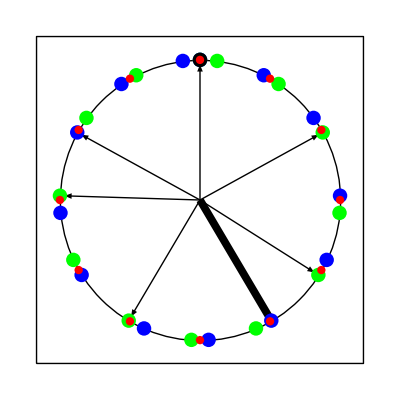

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 notesdebase[[4]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 notesdebase[[4]],{0,0}],PointSize[0.026],Green,Table[Point[{3 Cos[theta[quintesascendantes[[k]]]],3 Sin[theta[quintesascendantes[[k]]]]}],{k,1,13}],Blue,Table[Point[{3 Cos[theta[quartesascendantes [[k]]]],3 Sin[theta[quartesascendantes [[k]]]]}],{k,1,13}],Black,Point[{0,3}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

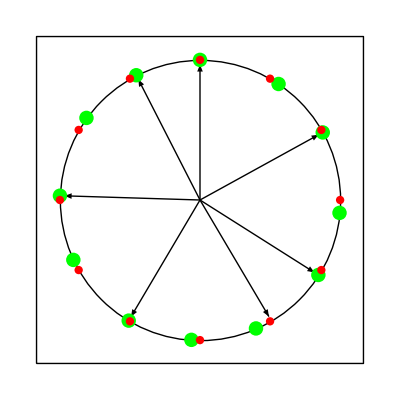

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,7}],PointSize[0.026],Green,Table[Point[{3 Cos[theta[quintesascendantes[[k]]]],3 Sin[theta[quintesascendantes[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

## Partition simplifiée

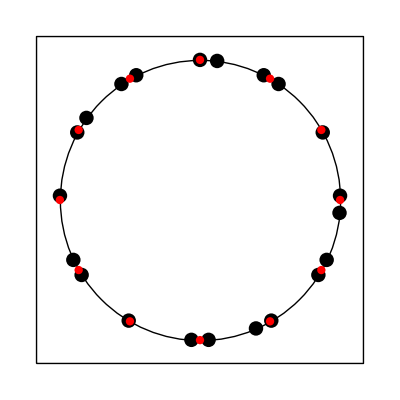

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Point[{3 Cos[theta[touteslesnotes[[k]]]],3 Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
tc=1200  Log[2,2187/2048];td=1200 Log[2,256/243];
```

```mathematica
5tc+7td//Simplify
```

1200

```mathematica
notesdebase=Most[Accumulate[{0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td}]]
```

{0,(1200 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2]}

```mathematica
touteslesnotes=Union[Join[notesdebase,Mod[notesdebase+tc,1200],Mod[notesdebase-tc,1200]]]
```

{0,1200-(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],-1200+(7200 Log[256/243])/Log[2]+(7200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2],(1200 Log[2187/2048])/Log[2]}

```mathematica
{Length[touteslesnotes],Sort[N[touteslesnotes]]}
```

{21,{0.,23.46,90.225,113.685,203.91,294.135,317.595,384.36,407.82,498.045,521.505,588.27,611.73,701.955,792.18,815.64,905.865,996.09,1019.55,1086.31,1109.78}}

```mathematica
Union[N[quartesascendantes],N[quintesascendantes]]
```

{0.,23.46,90.225,113.685,180.45,203.91,294.135,317.595,384.36,407.82,498.045,521.505,588.27,611.73,678.495,701.955,792.18,815.64,882.405,905.865,996.09,1019.55,1086.31,1109.78,1176.54}

```mathematica
Length[%]
```

25

```mathematica
touteslesnotes2=Union[Join[touteslesnotes,Mod[touteslesnotes+tc,1200],Mod[touteslesnotes-tc,1200]]]
```

{0,1200-(2400 Log[2187/2048])/Log[2],1200-(1200 Log[2187/2048])/Log[2],1200+(1200 Log[256/243])/Log[2]-(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(7200 Log[2187/2048])/Log[2],-1200+(7200 Log[256/243])/Log[2]+(7200 Log[2187/2048])/Log[2],-1200+(7200 Log[256/243])/Log[2]+(8400 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2],(2400 Log[256/243])/Log[2],(3600 Log[256/243])/Log[2],(1200 Log[2187/2048])/Log[2],(2400 Log[2187/2048])/Log[2]}

```mathematica
Length[%]
```

35

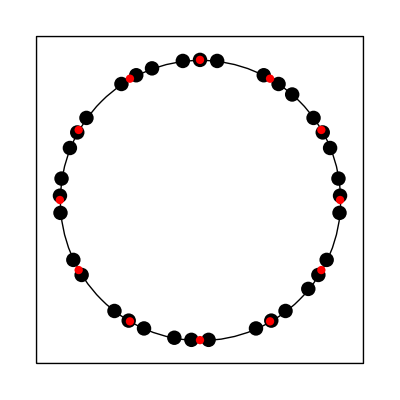

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Point[{3 Cos[theta[touteslesnotes2[[k]]]],3 Sin[theta[touteslesnotes2[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
touteslesnotes3=Union[Join[touteslesnotes2,Mod[touteslesnotes+tc,1200],Mod[touteslesnotes2-tc,1200]]]
```

{0,1200-(3600 Log[2187/2048])/Log[2],1200-(2400 Log[2187/2048])/Log[2],1200+(1200 Log[256/243])/Log[2]-(2400 Log[2187/2048])/Log[2],1200-(1200 Log[2187/2048])/Log[2],1200+(1200 Log[256/243])/Log[2]-(1200 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]-(1200 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]-(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(1200 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(2400 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(3600 Log[2187/2048])/Log[2],(2400 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(3600 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(4800 Log[2187/2048])/Log[2],(4800 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(7200 Log[256/243])/Log[2]+(6000 Log[2187/2048])/Log[2],(6000 Log[256/243])/Log[2]+(7200 Log[2187/2048])/Log[2],-1200+(7200 Log[256/243])/Log[2]+(7200 Log[2187/2048])/Log[2],-1200+(7200 Log[256/243])/Log[2]+(8400 Log[2187/2048])/Log[2],(1200 Log[256/243])/Log[2],(2400 Log[256/243])/Log[2],(3600 Log[256/243])/Log[2],(4800 Log[256/243])/Log[2],(1200 Log[2187/2048])/Log[2],(2400 Log[2187/2048])/Log[2]}

```mathematica
Length[%]
```

42

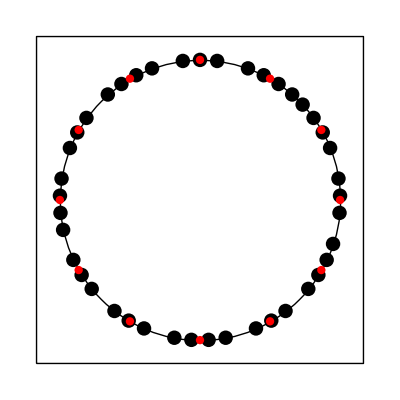

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Point[{3 Cos[theta[touteslesnotes3[[k]]]],3 Sin[theta[touteslesnotes3[[k]]]]}],{k,1,42}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

## Schéma de quintes ascendantes :

```mathematica
Table[(3/2)^k,{k,0,11}]//N
```

{1.,1.5,2.25,3.375,5.0625,7.59375,11.3906,17.0859,25.6289,38.4434,57.665,86.4976}

## Quintes ascendantes triées et ramenées à une octave unique :

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]
```

{1,531441/524288,2187/2048,9/8,19683/16384,81/64,177147/131072,729/512,3/2,6561/4096,27/16,59049/32768,243/128}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]
```

{1,3/2,9/8,27/16,81/64,243/128,729/512,2187/2048,6561/4096,19683/16384,59049/32768,177147/131072,531441/524288}

```mathematica
Ratios[{1,2187/2048,9/8,19683/16384,81/64,177147/131072,729/512,3/2,6561/4096,27/16,59049/32768,243/128,2}]
```

{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,256/243}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]
```

{1,3/2,9/8,27/16,81/64,243/128,729/512,2187/2048,6561/4096,19683/16384,59049/32768,177147/131072}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]//N
```

{1.,1.5,1.125,1.6875,1.26563,1.89844,1.42383,1.06787,1.60181,1.20135,1.80203,1.35152,1.01364}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]//N                 (*A comparer au schéma exactement tempéré*)
```

{1.,1.01364,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]//N                  (*Observer que le cycle ne se referme pas exactement : on dépasse 2, d'où la présence de 1.01364*)
```

{1.,1.01364,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]]          (*On ne trouve que deux intervalles : tc=1200Log[2,2187/2048]=90.225 et td=1200Log[2,256/243]=113.685*)
```

{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,35}]]]
```

{531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288}

```mathematica
{1200Log[2,531441/524288],1200Log[2,134217728/129140163],1200Log[2,70368744177664/68630377364883]}//N
```

{23.46,66.765,43.305}

```mathematica
3{23.460010384649014,66.7649852884139,43.304974903764894}/Total[{23.460010384649014,66.7649852884139,43.304974903764894}]
```

{0.527073,1.5,0.972927}

```mathematica
{1200Log[2,2187/2048],1200Log[2,256/243]}//N
```

{113.685,90.225}

```mathematica
113.68500605771193/90.22499567306305
```

1.26002

```mathematica
1200Log[2,#]&/@Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]]//N            (*Observer que le cycle ne se referme pas exactement : on dépasse 2*)
```

{23.46,90.225,90.225,113.685,90.225,113.685,90.225,90.225,113.685,90.225,113.685,90.225}

```mathematica
Total[{23.460010384649014,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305}]
```

1109.78

## Schéma de quintes descendantes :

```mathematica
Table[(3/2)^k,{k,0,-11,-1}]//N
```

{1.,0.666667,0.444444,0.296296,0.197531,0.131687,0.0877915,0.0585277,0.0390184,0.0260123,0.0173415,0.011561}

## Quintes descendantes ramenées à une octave unique :

```mathematica
Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]
```

{256/243,65536/59049,32/27,8192/6561,4/3,1024/729,262144/177147,128/81,32768/19683,16/9,4096/2187,2}

```mathematica
Ratios[Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]]
```

{256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,2187/2048}

```mathematica
{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}
```

## En résumé :

```mathematica
tc=1200  Log[2,2187/2048];td=1200 Log[2,256/243];
```

```mathematica
{tc,td,tc+ td,tc- td,2td-tc}//N
```

{113.685,90.225,203.91,23.46,66.765}

```mathematica
5tc+7td//Simplify
```

1200

```mathematica
intervMAJencents={0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td};
```

```mathematica
Accumulate[intervMAJencents]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78,1200.}

```mathematica
notesdebase=Most[Accumulate[intervMAJencents]]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78}

```mathematica
touteslesnotes=Sort[Join[notesdebase,Mod[notesdebase+tc,1200.],Mod[notesdebase-tc,1200.]]]
```

{0.,23.46,90.225,113.685,203.91,294.135,317.595,384.36,407.82,498.045,521.505,588.27,611.73,701.955,792.18,815.64,905.865,996.09,1019.55,1086.31,1109.78}

```mathematica
Length[touteslesnotes]
```

21

```mathematica
Append[Differences[touteslesnotes],90.22499567306306]
```

{23.46,66.765,23.46,90.225,90.225,23.46,66.765,23.46,90.225,23.46,66.765,23.46,90.225,90.225,23.46,90.225,90.225,23.46,66.765,23.46,90.225}

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

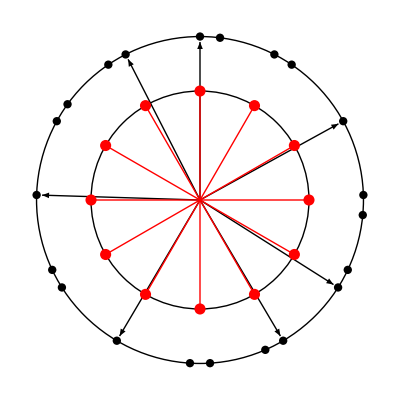

```mathematica
Graphics[{Circle[{0,0},2],Circle[{0,0},3],PointSize[0.015],Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,Table[Line[{{0,0},{2Cos[(2k π)/12],2Sin[(2k π)/12]}}],{k,0,11}],PointSize[0.02],Table[Point[{2Cos[(2k π)/12],2Sin[(2k π)/12]}],{k,0,11}]}]
```

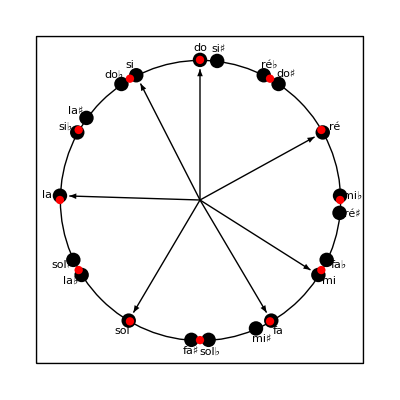

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[notes21[[k]],{3.28Cos[theta[touteslesnotes[[k]]]],3.25Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

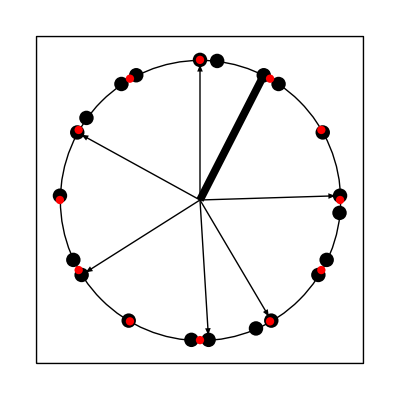

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[3]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[3]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
s[q_]:=Mod[300-600 q/π,1200]
```

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

```mathematica
s[theta[1.1]]
```

1.1

```mathematica
theta[905.87]
```

3.11086

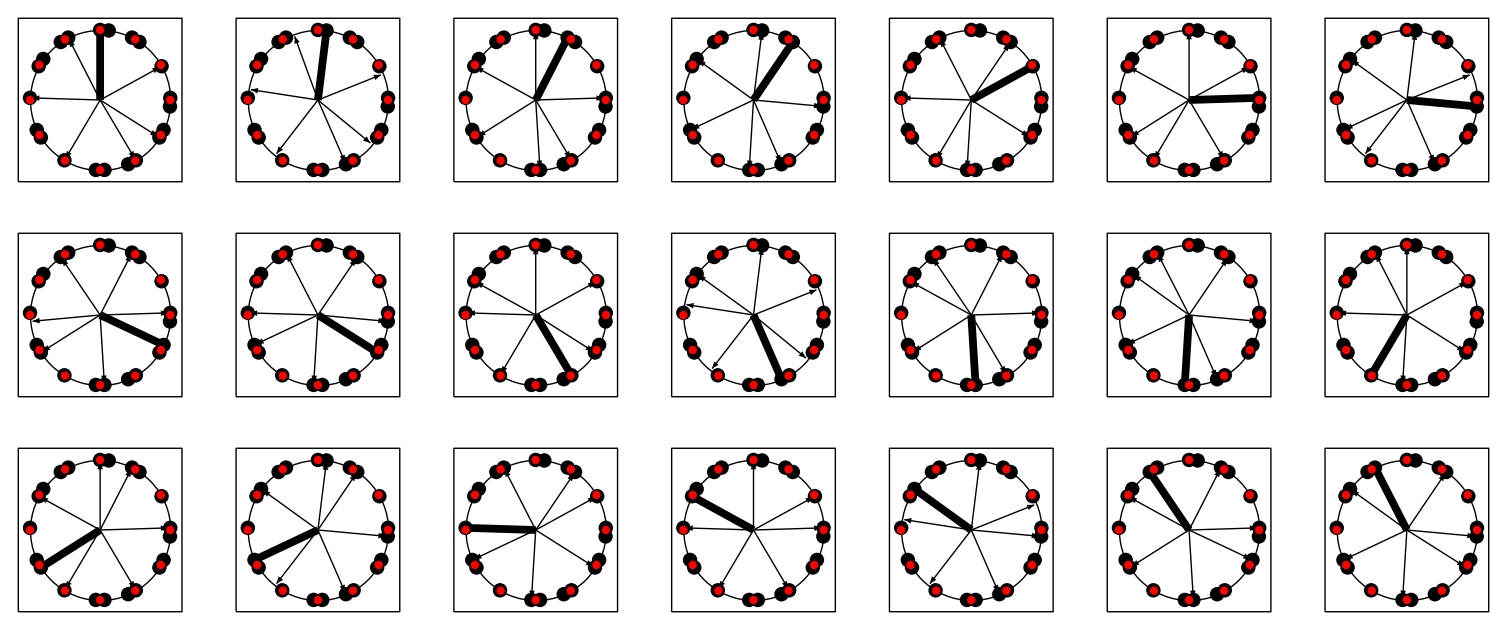

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[k]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[k]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{k,21}],7]]
```

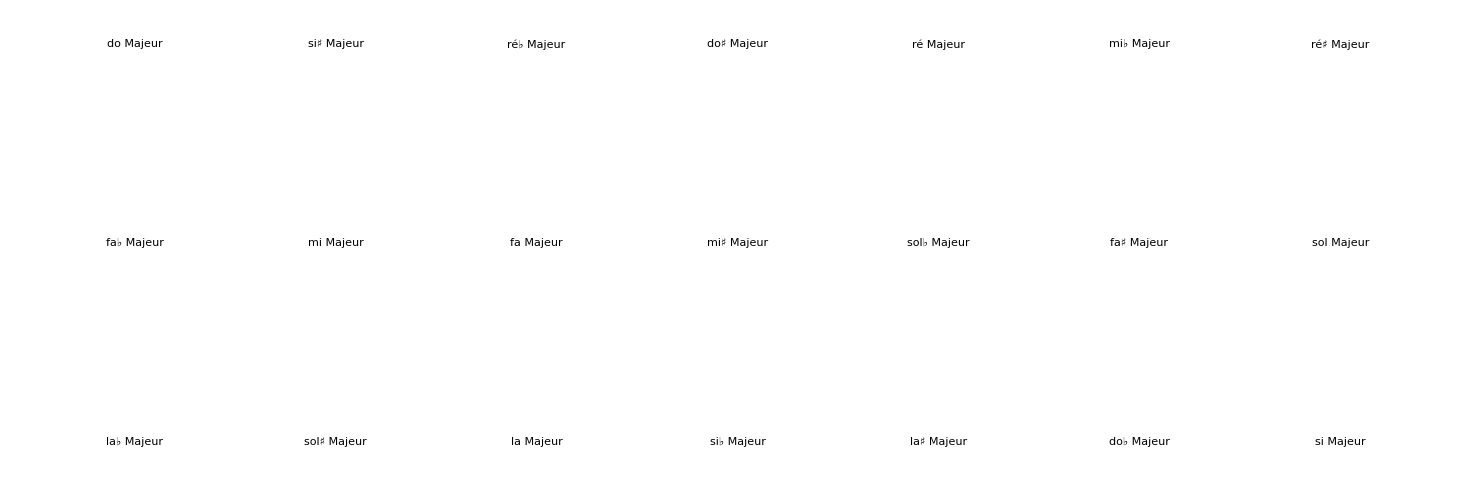

```mathematica
GraphicsGrid[Partition[Table[Labeled[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[k]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[k]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],modesmajeurs[[k]]],{k,21}],7]]
```

```mathematica
modesmajeurs={"do Majeur","si♯ Majeur","ré♭ Majeur","do♯ Majeur","ré Majeur","mi♭ Majeur","ré♯ Majeur","fa♭ Majeur","mi Majeur","fa Majeur","mi♯ Majeur","sol♭ Majeur","fa♯ Majeur","sol Majeur","la♭ Majeur","sol♯ Majeur","la Majeur","si♭ Majeur","la♯ Majeur","do♭ Majeur","si Majeur"}
```

{do Majeur,si♯ Majeur,ré♭ Majeur,do♯ Majeur,ré Majeur,mi♭ Majeur,ré♯ Majeur,fa♭ Majeur,mi Majeur,fa Majeur,mi♯ Majeur,sol♭ Majeur,fa♯ Majeur,sol Majeur,la♭ Majeur,sol♯ Majeur,la Majeur,si♭ Majeur,la♯ Majeur,do♭ Majeur,si Majeur}

```mathematica
notes21={"do","si♯","ré♭","do♯","ré","mi♭","ré♯","fa♭","mi","fa","mi♯","sol♭","fa♯","sol","la♭","sol♯","la","si♭","la♯","do♭","si"}
```

{do,si♯,ré♭,do♯,ré,mi♭,ré♯,fa♭,mi,fa,mi♯,sol♭,fa♯,sol,la♭,sol♯,la,si♭,la♯,do♭,si}